# Tutorial #3:

## Take a Deep Breath (Why Mathematica?)

Warmup: Activate help files (using ? or the [Help] -> [Documentation Center] Menu) and explore one other special function (e.g., Laguerre polynomials, Hermite polynomials, Legendre polynomials, hypergeometric functions).  Things to try might include plots, series expansions (e.g., near zero or infinity),  different choices of parameters or arguments, etc.

## Making Things Look Pretty

The brackets on the right side of the screen show groupings. Inputs are grouped with their respective outputs, and Mathematica also allows the creation of sections and subsections (and so on).

In addition, extra formatting options for exponents, fractions, etc can be found under Palettes-> Basic Math Assistant. Hovering over each of these options will give the respective keyboard shortcuts.

Exercise 0: instead of using the tutorial template this week,open up a new notebook and format it so that it shows:
Text | Style
Tutorial 3 | Title
<Today's Date> | Subtitle
<Your Name and NSID> | Subsubtitle
And three sections Warmup, Exercise 1, and Exercise 2 (don't create a section for Exercise 0).

## Mathematica As a Tool

Matlab | Matrix Manipulation and Interfacing
Python | Free and Has a Package for Everything
Maple | Canadian
Mathematica | Symbolic Manipulation

The reason why we use Mathematica is the powerful ability to manipulate equations and problems without having to use numbers.

## Introduction to Solving Equations

There’s lots of ways to solve equations using Mathematica:

```mathematica
?Solve
?NSolve
?Reduce
?FindRoot
```

RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to solve the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"Solve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["dom", "TI"]}], "]"}] solves over the domain StyleBox["dom", "TI"]. Common choices of StyleBox["dom", "TI"] are Reals, Integers, and Complexes.

RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] attempts to find numerical approximations to the solutions of the system StyleBox["expr", "TI"] of equations or inequalities for the variables StyleBox["vars", "TI"]. 
RowBox[{"NSolve", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", "Reals"}], "]"}] finds solutions over the domain of real numbers.

RowBox[{"Reduce", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"]}], "]"}] reduces the statement StyleBox["expr", "TI"] by solving equations or inequalities for StyleBox["vars", "TI"] and eliminating quantifiers. 
RowBox[{"Reduce", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["vars", "TI"], ",", StyleBox["dom", "TI"]}], "]"}] does the reduction over the domain StyleBox["dom", "TI"]. Common choices of StyleBox["dom", "TI"] are Reals, Integers, and Complexes.

RowBox[{"FindRoot", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}]}], "]"}] searches for a numerical root of StyleBox["f", "TI"], starting from the point RowBox[{StyleBox["x", "TI"], "=", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}].
RowBox[{"FindRoot", "[", RowBox[{RowBox[{StyleBox["lhs", "TI"], "==", StyleBox["rhs", "TI"]}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}]}], "]"}] searches for a numerical solution to the equation RowBox[{StyleBox["lhs", "TI"], "==", StyleBox["rhs", "TI"]}]. 
RowBox[{"FindRoot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["f", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["f", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a simultaneous numerical root of all the SubscriptBox[StyleBox["f", "TI"], StyleBox["i", "TI"]].
RowBox[{"FindRoot", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["eqn", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["eqn", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["y", "TI"], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["0", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] searches for a numerical solution to the simultaneous equations SubscriptBox[StyleBox["eqn", "TI"], StyleBox["i", "TI"]].

For most realistic cases, we'll use the FindRoot[ ] command, which deals with input numerically. Whenever we deal with solving numerical equations, whereever possible it's beneficial to plot your functions first to inspect any problematic regions (asymptotes, multiple solutions, etc)

```mathematica
Plot[{-Cot[z],Sqrt[z]},{z,0,2π}]
FindRoot[-Cot[z]==Sqrt[z],{z,π/4}]
```

Exercise 1: Find the smallest positive solution for tan(x) = √(z_0^2/z^2-1)

## Modules

```mathematica
?Module
```

Module[{x,y,…},expr] specifies that occurrences of the symbols x, y, … in expr should be treated as local. 
Module[{x=x_0,…},expr] defines initial values for x, ….

### Module Example

```mathematica
ηodd[z0_]:=Module[{sol},sol=z/.FindRoot[{-Cot[z]==Sqrt[z0^2/z^2-1]},{z,π/4}]; z0^2-sol]
```

```mathematica
ηeven[z0_]:=Module[{sol},sol=z/.FindRoot[{Tan[z]==Sqrt[z0^2/z^2-1]},{z,π/4}]; z0^2-sol]
```

```mathematica
Manipulate[Plot[{Tan[z],Sqrt[z0^2/z^2-1]},{z,0,6},Exclusions->{π/2,(3π)/2},PlotRange->{-10,15}],{z0,1,10}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

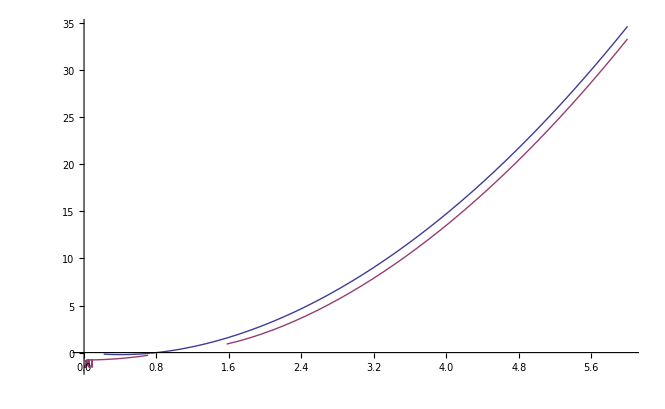

```mathematica
Plot[{ηeven[z0],ηodd[z0]},{z0,0,6}]
```

### Exercise

Exercise 2: Take the function

```mathematica
f[n_,x_, k_]:=∑_(k=0)^∞ ((-1)^k(x/2)^(n+2k))/(k!Gamma[n+k+1])
```

Create a module that takes 2 k values (with n=0), and outputs:
	⋆ A graph of the functions on the same set of axes,
	⋆ The x-value of the first intersection of the functions,
	⋆ The y-value of the intersection.

Reminder: Include name in Mathematica notebook, with a filename lastnamefirstinitial_Tutorial3.nb (eg. HoJ_Tutorial3.nb) and email the completed notebook to j.ho@example.ca